# Analytics and numerical simulations for direct emission-based schemes

## Simulations of Bell-pair/GHZ - Single-Click (Raw), Bell-pair/GHZ-Double-Click, W-state protocols

## Siddhant Singh, QuTech, TU Delft Contact @ siddhant.singh@tudelft.nl

## (Synced to GitHub repository of Direct Emission Based Scheme. See: https://github.com/siddhantphy/emission_direct_scheme ) Contributions

Siddhant Singh: Full development of all the four protocols (Raw (single-click), double-click, basic, medium)
Kazufumi Tanji: Analytical POVM calculations for GHZ and W states
Rikiya Kashiwagi: Mathematica implementation of POVM elements’ matrices
Daniel Bhatti: Theoretical analysis of W to GHZ protocol

### Notes

Development and compatibility: Developed and tested in Wolfram Mathematica 14.1.
Runtime: The whole notebook evaluates in approximately:
- 14 min 20 s using “Evaluate Notebook” command on Intel Core-i7 vPro
- 7 min 26 s by running cells manually on Intel Core-i7 vPro (Not sure why the difference!)

## Section-1: Paclets used

```mathematica
(*PacletInstall["Wolfram/QuantumFramework"];*)
(* First uncomment and run the paclet installer command above, if running for the first time! *)
Needs["Wolfram`QuantumFramework`"];
```

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`SecondQuantization`
```

## Section-2: Physical model assumptions

1) No more than one photon comes from the same user (no double excitation involved), however double excitation error upon emission is considered and it is assumed that the photon is lost, modelled as pure dephasing effect.
2) Bell pair parameters take into account the quality of quantum memory and entanglement generation.
3) The photon detectors can be photon number resolving and non-photon number resolving.
4) Dark counts for these emission-based setups are very low and are neglected in our hardware modelling.
5) ...

## Section-3: Input parameters

```mathematica
ClearAll[η,α,μ,Fprep,pEE,pg,λ];

(* Hardware parameters *)
η=Symbol["η"];
α=Symbol["α"];
μ=Symbol["μ"];
λ=Symbol["λ"];
Fprep=Symbol["Fprep"];
pEE=Symbol["pEE"];
pg=Symbol["pg"];
```

```mathematica
(* Theoretical assumption on photon number counting for the detectors *)
(* PNRS: Photon Number Resolving *)
(*DetectorType = "PNR";*)
DetectorType = "NON-PNR";

(* Numerical assumptions *)
$Assumptions =Element[{α,Fprep,λ,η,μ,pEE,pg},Reals]&& 0<=α<=1 && 0<=pg<=1 && 0<=λ<=1 && 0<=pEE<=1 && 0<=Fprep<=1&& 0<=η<=1&& 0<=μ<=1;

(* Input parameter numerical values *)
SetZeroNoise = {α->0.02,μ->1,Fprep->1,pEE->0,pg->0,η->1,λ->1};
SetNVnoGateError = {α->0.02,μ->0.95,Fprep->0.999,pEE->0.01,pg->0,λ->0.8};
SetNVPg1 = {α->0.02,μ->0.95,Fprep->0.999,pEE->0.01,pg->0.001,λ->1,η->0.4472};
SetOnlyη = {α->0.02,μ->1,Fprep->1,pEE->0,pg->0,λ->1};
SetFP = {α->0.05,μ->0.95,Fprep->0.999,pEE->0.01,pg->0.001,λ->1,η->0.4472};
SetFPDC = {α->0.5,μ->0.95,Fprep->0.999,pEE->0.01,pg->0.001,λ->1,η->0.4472};
(*Function to assign values dynamically*)
AssignValuesFromSets[list_]:=(Evaluate[First[#]]=Last[#])&/@list;
```

## Section-4: Define functions and operators

### Photonic operators and state

```mathematica
SetFockSpaceSize[2];
(* b=AnnihilationOperator[];*)
```

### Target states

```mathematica
(* We assume the target GHZ state to be the one that corresponds to the measurement with detector 1 and 2 detecting photons! *)
TargetBell1=QuantumState["PsiMinus"];
TargetBell2=QuantumState["PsiPlus"];
TargetBell3=QuantumState["PhiPlus"];
TargetGHZ1=1/(√2)(QuantumState["0101"]+QuantumState["1010"]);
TargetGHZ2=1/(√2)(QuantumState["0101"]-QuantumState["1010"]);
TargetGHZ3=1/(√2)(QuantumState["0000"]-QuantumState["1111"]);
TargetGHZ4=QuantumState["GHZ"[4]];
Wstate4=QuantumState["W"[4]];
```

### Fidelity function for two quantum states

```mathematica
(* Note that ρ and σ are valid `QuantumState` objects in Quantum Framework *)
(* Own function for fidelity calculation! *)
QFidelity[ρ_,σ_]:=Tr[MatrixPower[MatrixPower[ρ["DensityMatrix"],1/2].σ["DensityMatrix"].MatrixPower[ρ["DensityMatrix"],1/2],1/2]];
```

### POVM elements for photon detection for Bell-pair setup

We consider the set of measurement operators based on the outcome elements. We focus on the scenarios where only the detector-1 or detector-2 click. We assume all modes have mutual photon visibility factor of , where   is real and . The Kraus operators are directly shown below!

```mathematica
(* We directly encode the corresponding Kraus operators for the POVM elements *)
k00={{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
k10=(1/2){{0,0,0,0},{0,(√(1+μ)+√(1-μ))/√2,(√(1+μ)-√(1-μ))/√2,0},{0,(√(1+μ)-√(1-μ))/√2,(√(1+μ)+√(1-μ))/√2,0},{0,0,0,√(1+μ^2)}};
k01=(1/2){{0,0,0,0},{0,(√(1+μ)+√(1-μ))/√2,(-√(1+μ)+√(1-μ))/√2,0},{0,(-√(1+μ)+√(1-μ))/√2,(√(1+μ)+√(1-μ))/√2,0},{0,0,0,√(1+μ^2)}};
k11=(1/√2){{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,√(1-μ^2)}};
```

### POVM elements for photon detection for Bell-pair setup (for photon number resolving case)

```mathematica
M10PNR = (1/2){{0,0,0,0},{0,1,μ,0},{0,μ,1,0},{0,0,0,0}};
M01PNR = (1/2){{0,0,0,0},{0,1,-μ,0},{0,-μ,1,0},{0,0,0,0}};

(* Kraus operators for relevant detetcor pattern *)
k10PNR = MatrixPower[M10PNR,1/2];
k01PNR = MatrixPower[M01PNR,1/2];
```

```mathematica
kb10=Module[{},If[DetectorType=="PNR",k10PNR,k10]];
kb01=Module[{},If[DetectorType=="PNR",k01PNR,k01]];
```

### POVM elements for photon detection for direct-emission setup (weight-4 GHZ state)

We consider the set of measurement operators based on the outcome elements. We focus on the scenarios where only the detector-1 and detector-2 click. These include:

These measurement operators are taken from calculations of Kazufumi Tanji. We eventually assume all modes have mutual photon visibility factor of , where   is real and .

```mathematica
(* Define replacement rules for μ *)
GroupS3=GroupElements[SymmetricGroup[3]];
GroupS4=GroupElements[SymmetricGroup[4]];
MuRule1=Table[Indexed[μ,{i,i}]->1,{i,4}];
MuRule2=Flatten[Table[Indexed[μ,{j,i}]->Indexed[μ,{i,j}],{i,4},{j,i+1,4}]];
ApplyMuRule[Mat_]:=Mat/.MuRule1/.MuRule2;
```

```mathematica
M1100=M1200=M2100=M2200=M1300=M3100=Table[0,{16},{16}];

(* M1100 *)
For[Subscript[n, 1]=1,Subscript[n, 1]<=4,Subscript[n, 1]++,
For[Subscript[n, 2]=Subscript[n, 1]+1,Subscript[n, 2]<=4,Subscript[n, 2]++,
For[Subscript[m, 1]=1,Subscript[m, 1]<=4,Subscript[m, 1]++,
For[Subscript[m, 2]=Subscript[m, 1]+1,Subscript[m, 2]<=4,Subscript[m, 2]++,
M1100[[2^(4-Subscript[n, 1])+2^(4-Subscript[n, 2])+1,2^(4-Subscript[m, 1])+2^(4-Subscript[m, 2])+1]]+=((-1)^(Subscript[n, 1]+Subscript[m, 1])+(-1)^(Subscript[n, 2]+Subscript[m, 2]))*Indexed[μ,{Subscript[n, 1],Subscript[m, 1]}]*Indexed[μ,{Subscript[n, 2],Subscript[m, 2]}]
+((-1)^(Subscript[n, 1]+Subscript[m, 2])+(-1)^(Subscript[n, 2]+Subscript[m, 1]))*Indexed[μ,{Subscript[n, 2],Subscript[m, 1]}]*Indexed[μ,{Subscript[n, 1],Subscript[m, 2]}]]]]];
M1100/=16;
M1100=ApplyMuRule[M1100]//Simplify;

(* M1200 *)
For[Subscript[n, 1]=1,Subscript[n, 1]<=4,Subscript[n, 1]++,
For[Subscript[n, 2]=Subscript[n, 1]+1,Subscript[n, 2]<=4,Subscript[n, 2]++,
For[Subscript[n, 3]=Subscript[n, 2]+1,Subscript[n, 3]<=4,Subscript[n, 3]++,
For[Subscript[m, 1]=1,Subscript[m, 1]<=4,Subscript[m, 1]++,
For[Subscript[m, 2]=Subscript[m, 1]+1,Subscript[m, 2]<=4,Subscript[m, 2]++,
For[Subscript[m, 3]=Subscript[m, 2]+1,Subscript[m, 3]<=4,Subscript[m, 3]++,
Map[Function[σ,
M1200[[2^(4-Subscript[n, 1])+2^(4-Subscript[n, 2])+2^(4-Subscript[n, 3])+1,2^(4-Subscript[m, 1])+2^(4-Subscript[m, 2])+2^(4-Subscript[m, 3])+1]]+=(-1)^(Subscript[n,PermutationReplace[2,σ[[1]]]]+Subscript[n,PermutationReplace[3,σ[[1]]]]+Subscript[m,PermutationReplace[2,σ[[2]]]]+Subscript[m,PermutationReplace[3,σ[[2]]]])*Product[Indexed[μ,{Subscript[n,PermutationReplace[i,σ[[1]]]],Subscript[m,PermutationReplace[i,σ[[2]]]]}],{i,3}]
],Tuples[{GroupS3,GroupS3}]]
]]]]]];
M1200/=64;
M1200=ApplyMuRule[M1200]//Simplify;

(* M2100 *)
For[Subscript[n, 1]=1,Subscript[n, 1]<=4,Subscript[n, 1]++,
For[Subscript[n, 2]=Subscript[n, 1]+1,Subscript[n, 2]<=4,Subscript[n, 2]++,
For[Subscript[n, 3]=Subscript[n, 2]+1,Subscript[n, 3]<=4,Subscript[n, 3]++,
For[Subscript[m, 1]=1,Subscript[m, 1]<=4,Subscript[m, 1]++,
For[Subscript[m, 2]=Subscript[m, 1]+1,Subscript[m, 2]<=4,Subscript[m, 2]++,
For[Subscript[m, 3]=Subscript[m, 2]+1,Subscript[m, 3]<=4,Subscript[m, 3]++,
Map[Function[σ,
M2100[[2^(4-Subscript[n, 1])+2^(4-Subscript[n, 2])+2^(4-Subscript[n, 3])+1,2^(4-Subscript[m, 1])+2^(4-Subscript[m, 2])+2^(4-Subscript[m, 3])+1]]+=(-1)^(Subscript[n,PermutationReplace[3,σ[[1]]]]+Subscript[m,PermutationReplace[3,σ[[2]]]])*Product[Indexed[μ,{Subscript[n,PermutationReplace[i,σ[[1]]]],Subscript[m,PermutationReplace[i,σ[[2]]]]}],{i,3}]
],Tuples[{GroupS3,GroupS3}]]
]]]]]];
M2100/=64;
M2100=ApplyMuRule[M2100]//Simplify;

(* M2200 *)
Map[Function[σ,
M2200[[16,16]]+=(-1)^(PermutationReplace[3,σ[[1]]]+PermutationReplace[4,σ[[1]]]+PermutationReplace[3,σ[[2]]]+PermutationReplace[4,σ[[2]]])*Product[Indexed[μ,{PermutationReplace[i,σ[[1]]],PermutationReplace[i,σ[[2]]]}],{i,4}];
],Tuples[{GroupS4,GroupS4}]];
M2200/=1024;
M2200=ApplyMuRule[M2200]//Simplify;

(* M1300 *)
Map[Function[σ,
M1300[[16,16]]+=(-1)^(PermutationReplace[2,σ[[1]]]+PermutationReplace[3,σ[[1]]]+PermutationReplace[4,σ[[1]]]+PermutationReplace[2,σ[[2]]]+PermutationReplace[3,σ[[2]]]+PermutationReplace[4,σ[[2]]])*Product[Indexed[μ,{PermutationReplace[i,σ[[1]]],PermutationReplace[i,σ[[2]]]}],{i,4}];
],Tuples[{GroupS4,GroupS4}]];
M1300/=256*6;
M1300=ApplyMuRule[M1300]//Simplify;

(* M3100 *)
Map[Function[σ,
M3100[[16,16]]+=(-1)^(PermutationReplace[4,σ[[1]]]+PermutationReplace[4,σ[[2]]])*Product[Indexed[μ,{PermutationReplace[i,σ[[1]]],PermutationReplace[i,σ[[2]]]}],{i,4}];
],Tuples[{GroupS4,GroupS4}]];
M3100/=256*6;
M3100=ApplyMuRule[M3100]//Simplify;
```

Now we apply the assumption of identical pair-wise photon indistinguishability, taken to be μ for all modes’ pairs.

```mathematica
Identicalμ=Flatten[Table[Indexed[μ,{i,j}]->μ,{i,4},{j,i+1,4}]];
M1100=M1100/.Identicalμ//Simplify;
M1200=M1200/.Identicalμ//Simplify;
M2100=M2100/.Identicalμ//Simplify;
M2200=M2200/.Identicalμ//Simplify;
M1300=M1300/.Identicalμ//Simplify;
M3100=M3100/.Identicalμ//Simplify;
```

```mathematica
(* Convert these to `SparseArray` for faster computation! *)
(*M1100=SparseArray[M1100];
M1200=SparseArray[M1200];
M2100=SparseArray[M2100];
M2200=SparseArray[M2200];
M1300=SparseArray[M1300];
M3100=SparseArray[M3100];*)
```

Implementation non-photon counter detectors:
We add the POVM matrices that correspond to the detection within the same detectors

```mathematica
Md1d2=Module[{},If[DetectorType=="PNR",Simplify[M1100],Simplify[M1100+M1200+M2100+M2200+M1300+M3100]]]; (* All events that lead to both detector-1 and detector-2 clicking *)
```

Kraus operator based on this POVM element:

```mathematica
Kd1d2=MatrixPower[Md1d2,1/2];
```

### POVM elements for photon detection for direct-emission setup (weight-4 W state)

We consider the set of measurement operators based on the outcome elements. We focus on the scenarios where only the detector-1 clicks. These include: 
We again eventually assume all modes have mutual photon visibility factor of , where   is real and  as for the case of GHZ generation!

```mathematica
MW1000=MW2000=MW3000=MW4000=Table[0,{16},{16}];

For[Subscript[n, 1]=1,Subscript[n, 1]<=4,Subscript[n, 1]++,
For[Subscript[m, 1]=1,Subscript[m, 1]<=4,Subscript[m, 1]++,
MW1000[[2^(4-Subscript[n, 1])+1,2^(4-Subscript[m, 1])+1]]+=Indexed[μ,{Subscript[n, 1],Subscript[m, 1]}] ]];
MW1000/=4;
MW1000=ApplyMuRule[MW1000]//Simplify;

MW2000=Table[0,{16},{16}];
For[Subscript[n, 1]=1,Subscript[n, 1]<=4,Subscript[n, 1]++,
For[Subscript[n, 2]=Subscript[n, 1]+1,Subscript[n, 2]<=4,Subscript[n, 2]++,
For[Subscript[m, 1]=1,Subscript[m, 1]<=4,Subscript[m, 1]++,
For[Subscript[m, 2]=Subscript[m, 1]+1,Subscript[m, 2]<=4,Subscript[m, 2]++,
Map[Function[σ, MW2000[[2^(4-Subscript[n, 1])+2^(4-Subscript[n, 2])+1,2^(4-Subscript[m, 1])+2^(4-Subscript[m, 2])+1]]+=Product[Indexed[μ,{Subscript[n,PermutationReplace[i,σ]],Subscript[m,PermutationReplace[i,σ]]}]*Indexed[μ,{Subscript[n, 2],Subscript[m, 2]}],{i,2}]],GroupS2]]]]];
MW2000/=32;
MW2000=ApplyMuRule[MW2000]//Simplify;

Mat3000=Table[0,{16},{16}];
For[Subscript[n, 1]=1,Subscript[n, 1]<=4,Subscript[n, 1]++,
For[Subscript[n, 2]=Subscript[n, 1]+1,Subscript[n, 2]<=4,Subscript[n, 2]++,
For[Subscript[n, 3]=Subscript[n, 2]+1,Subscript[n, 3]<=4,Subscript[n, 3]++,
For[Subscript[m, 1]=1,Subscript[m, 1]<=4,Subscript[m, 1]++,
For[Subscript[m, 2]=Subscript[m, 1]+1,Subscript[m, 2]<=4,Subscript[m, 2]++,
For[Subscript[m, 3]=Subscript[m, 2]+1,Subscript[m, 3]<=4,Subscript[m, 3]++,
Map[Function[σ,
MW3000[[2^(4-Subscript[n, 1])+2^(4-Subscript[n, 2])+2^(4-Subscript[n, 3])+1,2^(4-Subscript[m, 1])+2^(4-Subscript[m, 2])+2^(4-Subscript[m, 3])+1]]+=Product[Indexed[μ,{Subscript[n,PermutationReplace[i,σ[[1]]]],Subscript[m,PermutationReplace[i,σ[[2]]]]}],{i,3}]
],Tuples[{GroupS3,GroupS3}]]
]]]]]];
MW3000/=384;
MW3000=ApplyMuRule[MW3000]//Simplify;

MW4000=Table[0,{16},{16}];
Map[Function[σ,
MW4000[[16,16]]+=Product[Indexed[μ,{PermutationReplace[i,σ[[1]]],PermutationReplace[i,σ[[2]]]}],{i,4}];
],Tuples[{GroupS4,GroupS4}]];
MW4000/=256*24;
MW4000=ApplyMuRule[MW4000]//Simplify;
```

Now we apply the assumption of identical pair-wise photon indistinguishability, taken to be μ for all modes’ pairs.

```mathematica
Identicalμ=Flatten[Table[Indexed[μ,{i,j}]->μ,{i,1,4},{j,1,4}]];
MW1000=MW1000/.Identicalμ//Simplify;
MW2000=MW2000/.Identicalμ//Simplify;
MW3000=MW3000/.Identicalμ//Simplify;
MW4000=MW4000/.Identicalμ//Simplify;
```

Implementation non-photon counter detectors:
We add the POVM matrices that correspond to the detection within the same detector

```mathematica
MWd1 = Module[{},If[DetectorType=="PNR",Simplify[MW1000],Simplify[MW1000+MW2000+MW3000+MW4000]]];
```

Kraus operator based on this POVM element:

```mathematica
kWd1=MatrixPower[MWd1,1/2];
```

## Section-5: Creating a Bell-pair between two modules with single-click (SC) protocol

### Step 0: Initialize the spins’ state with bright-state parameter

```mathematica
(* Initialize each emitter module in a target state with bright-state parameter `α` *)
ψBell0init=QuantumState[{Sqrt[1-α],Sqrt[α]},2];

(* Apply the emitter state preparation error as dephasing channel with parameter `Fprep` *)
ρBell0=Simplify[QuantumChannel["PhaseFlip"[1-Fprep],{1}][ψBell0init]];
```

### Step 1: Excite and create the four node emitter-photon states

```mathematica
(* Note that the CNOT operation in the following is taken to be noiseless, excitation error is added later as pure dephasing contribution! *)
ρBell1=QuantumOperator["CNOT",{2,4}][QuantumOperator["CNOT",{1,3}][QuantumTensorProduct[ρBell0,ρBell0,FockState[0],FockState[0]]]];
```

```mathematica
(* Now apply the double excitation error on the emitter photons with parameter `pEE` *)
ρBell1EE=Simplify[QuantumChannel["PhaseFlip"[pEE],{3,4}][ρBell1]];
```

### Step 2: Phase due to the path difference (modeled as dephasing) (λ)

```mathematica
ρBell2λ=Simplify[QuantumChannel["PhaseFlip"[1-λ],{3}][ρBell1EE]];
```

### Step 3: Photon loss before detection (η)

State ordered as |emitter-1⟩|emitter-2⟩|ph-1⟩|ph-2⟩
Then apply amplitude damping to the two photonic degrees of freedom!

```mathematica
ρBell3=Simplify[QuantumChannel["AmplitudeDamping"[1-η],{3,4}][ρBell2λ]];
```

### Step 4: Photon detection

```mathematica
(* Apply the Kraus operator operator. Note that here it is applied as `QuantumOperator`. Here we only apply for one detector, because
of the symmetry of the protocol. *)
ρBell4=QuantumOperator[kb10,{3,4}][ρBell3];

(* Success probability of desired detection pattern *)
PSuccBellRaw=Simplify[Tr[ρBell4]];

(* Normalize the state *)
ρBell4=Simplify[ρBell4/PSuccBellRaw];

(* Both detection patterns are equivalent, so we add up the success probabilities! *)
PSuccBellRaw=2 PSuccBellRaw;
```

### Step 5: Entangled Bell-state of emitters

```mathematica
ρBell5emitters=FullSimplify[QuantumPartialTrace[ρBell4,{3,4}]];
```

Calculate the fidelity w.r.t. target state

```mathematica
FidelityBellRaw=1-QuantumDistance[TargetBell2,ρBell5emitters,"Fidelity"]//Simplify;
```

### Raw Bell state results

Display the success probability

```mathematica
PSuccBellRaw//TraditionalForm
```

1/2 α η (α η (μ^2-3)+4)

Display the fidelity

```mathematica
FidelityBellRaw//TraditionalForm
```

√2 √(-((α-1) ((1-2 Fprep)^2 (2 λ-1) μ (1-2 pEE)^2+1))/(α η (μ^2-3)+4))

We convert the state to  target state by applying noiseless Pauli corrections, only for the convenience of stabilizer simulations use!

```mathematica
ρBell5emittersUsage=QuantumOperator["X",{2}][ρBell5emitters];
```

Export the density matrix to Python format!

```mathematica
(*Export["RhoBell5emittersUsage.txt",ρBell5emittersUsage["DensityMatrix"]//ArrayRules];
PythonConvert = StringReplace[Import["RhoBell5emittersUsage.txt"], {"λ"->"labda","^" -> "**", "μ" -> "mu", "Fprep" -> "F_prep", "pEE" -> "p_DE", "η" -> "eta", "α" -> "alpha","{" ~~ m : DigitCharacter .. ~~ ", " ~~ n : DigitCharacter .. ~~ "} ->" :> 
    "noisy_density_matrix[" <> ToString[ToExpression[m] - 1] <> "," <> ToString[ToExpression[n] - 1] <> "] ="}];
Export["RhoBell5emittersUsage.txt",PythonConvert];*)
```

Open the file to copy paste the Python expression

```mathematica
(*SystemOpen["RhoBell5emittersUsage.txt"];*)
```

## Section-6: Bell-pair between two modules with double-click (DC) protocol

We start this protocol from the raw state generated by the single-click protocol.
(We can also set α=1/2, which we already found via a separate optimization (supremum) of success probability of double click protocol.)
Also, λ=0 is set because of the symmetry of the protocol! The phase uncertainty gets eliminated.

```mathematica
(*α=1/2;*)
λ=0;
```

### Step 6: Flip the states of the emitters

```mathematica
ρBell6=QuantumOperator["X",{1,2}][ρBell5emitters];
```

These gates have a gate-error with physical error probability of

```mathematica
(* We apply a depolarizing channel to model this gate-error (circuit-level noise modelling) for all the X-gates applied! *)
ρBell6pg=Simplify[QuantumChannel["Depolarizing"[pg],{1,2}][ρBell6]];
```

### Step 7: Excite and create the four node emitter-photon states

```mathematica
(* Note that the CNOT operation in the following is taken to be noiseless, excitation error is added later as pure dephasing contribution! *)
ρBell7=QuantumOperator["CNOT",{2,4}][QuantumOperator["CNOT",{1,3}][QuantumTensorProduct[ρBell6pg,FockState[0],FockState[0]]]];
```

```mathematica
(* Now apply the double excitation error on the emitter photons with parameter `pEE` *)
ρBell7EE=Simplify[QuantumChannel["PhaseFlip"[pEE],{3,4}][ρBell7]];
```

### Step 8: Photon loss before detection (η)

State ordered as |emitter-1⟩|emitter-2⟩|ph-1⟩|ph-2⟩
Then apply amplitude damping to the two photonic degrees of freedom!

```mathematica
ρBell8=Simplify[QuantumChannel["AmplitudeDamping"[1-η],{3,4}][ρBell7EE]];
```

### Step 9: Photon detection

```mathematica
(* Apply the Kraus operator operator. Note that here it is applied as `QuantumOperator`. Here we only apply for one detector, because
of the symmetry of the protocol. *)
ρBell9=QuantumOperator[kb10,{3,4}][ρBell8];

(* Success probability of desired detection pattern *)
PSuccBellRaw2= Simplify[Tr[ρBell9]];

(* Normalize the state *)
ρBell9=Simplify[ρBell9/PSuccBellRaw2];

(* Both detection patterns are equivalent, so we add up the success probabilities! *)
PSuccBellRaw2= 2 PSuccBellRaw2;
```

Total success probability of the double-click protocol is the product of the two success probabilities

```mathematica
PSuccBellDC=Simplify[PSuccBellRaw PSuccBellRaw2];
```

### Step 10: Entangled Bell-state of emitters

```mathematica
ρBell10emitters=FullSimplify[QuantumPartialTrace[ρBell9,{3,4}]];
```

Calculate the fidelity w.r.t. target state

```mathematica
FidelityBellDC=1-QuantumDistance[TargetBell1,ρBell10emitters,"Fidelity"]//Simplify;
```

### Double-click state results

Display the success probability

```mathematica
PSuccBellDC//TraditionalForm
```

1/16 α η^2 (α (η (μ^2-3) pg^2 (η (μ^2-3)+8)+32 pg-32)-4 η (μ^2-3) pg^2+8 η (μ^2-3) pg+32)

Display the fidelity

```mathematica
FidelityBellDC/.α->1/2//TraditionalForm
```

√2 Re(√(-(-4 ((1-2 Fprep)^2 μ^2 (1-2 pEE)^4+1)+pg^2 (4 ((1-2 Fprep)^2 μ^2 (1-2 pEE)^4+1)-4 (2 (1-2 Fprep)^2 μ^2 (1-2 pEE)^4+1)+1/2 η (μ^2-3))-2 pg (4 ((1-2 Fprep)^2 μ^2 (1-2 pEE)^4+1)-4 (2 (1-2 Fprep)^2 μ^2 (1-2 pEE)^4+1)+1/2 η (μ^2-3)))/(-4 η (μ^2-3) pg^2+1/2 (η (μ^2-3) pg^2 (η (μ^2-3)+8)+32 pg-32)+8 η (μ^2-3) pg+32)))

```mathematica
(* In the absence of gate error *)
FidelityBellDC/.{α->1/2,pg->0}//TraditionalForm
```

(Re(√((1-2 Fprep)^2 μ^2 (1-2 pEE)^4+1)))/(√2)

We convert the state to  target state by applying noiseless Pauli corrections, only for the convenience of stabilizer simulations use!

```mathematica
ρBell10emittersUsage=QuantumOperator["Z",{2}][QuantumOperator["X",{2}][ρBell10emitters]];
```

```mathematica
ClearAll[λ];
λ=Symbol["λ"];
```

Export the density matrix to Python format!

```mathematica
(*Export["RhoBell10emittersUsage.txt",ρBell10emittersUsage["DensityMatrix"]//ArrayRules];
PythonConvert = StringReplace[Import["RhoBell10emittersUsage.txt"], {"^" -> "**", "μ" -> "mu", "Fprep" -> "F_prep", "pEE" -> "p_DE", "η" -> "eta", "α" -> "alpha","{" ~~ m : DigitCharacter .. ~~ ", " ~~ n : DigitCharacter .. ~~ "} ->" :> 
    "double_click_bell_pair[" <> ToString[ToExpression[m] - 1] <> "," <> ToString[ToExpression[n] - 1] <> "] ="}];
Export["RhoBell10emittersUsage.txt",PythonConvert];*)
```

Open the file to copy paste the Python expression

```mathematica
(*SystemOpen["RhoBell10emittersUsage.txt"];*)
```

## Section-7: Creating a direct GHZ state (Raw) between four modules with single-click (SC) protocol

### Step 0: Initialize the spins’ state with bright-state parameter

```mathematica
(* Initialize each emitter module in a target state with bright-state parameter `α` *)
ψ0init=QuantumState[{Sqrt[1-α],Sqrt[α]},2];

(* Apply the emitter state preparation error as dephasing channel with parameter `Fprep` *)
ρ0=Simplify[QuantumChannel["PhaseFlip"[1-Fprep],{1}][ψ0init]];
```

### Step 1: Excite and create the four node emitter-photon states

```mathematica
(* Note that the CNOT operation in the following is taken to be noiseless, excitation error is added later as pure dephasing contribution! *)
ρ1=QuantumOperator["CNOT",{4,8}][QuantumOperator["CNOT",{3,7}][QuantumOperator["CNOT",{2,6}][QuantumOperator["CNOT",{1,5}][QuantumTensorProduct[ρ0,ρ0,ρ0,ρ0,FockState[0],FockState[0],FockState[0],FockState[0]]]]]];
```

```mathematica
(* Now apply the double excitation error on the emitter photons with parameter `pEE` *)
ρ1EE=Simplify[QuantumChannel["PhaseFlip"[pEE],{5,6,7,8}][ρ1]];
```

### Step 2: Photon loss before detection (η)

State ordered as |emitter-1⟩|emitter-2⟩|emitter-3⟩|emitter-4⟩|ph-1⟩|ph-2⟩|ph-3⟩|ph-4⟩
Then apply amplitude damping to the last four photonic degrees of freedom

```mathematica
ρ2=Simplify[QuantumChannel["AmplitudeDamping"[1-η],{5,6,7,8}][ρ1EE]];
```

### Step 3: Photon detection

```mathematica
(* Apply the Kraus operator operator. Note that here it is applied as `QuantumOperator` because we have only one such operator, and
not full set of complete Kraus operators for the photon detection channel. *)
ρ3=QuantumOperator[Kd1d2,{5,6,7,8}][ρ2];

(* Success probability of desired detection pattern *)
PSuccRaw=Simplify[Tr[ρ3]];

(* Normalize the state *)
ρ3=Simplify[ρ3/PSuccRaw];
```

### Step 4: Entangled state of emitters

```mathematica
ρ4emitters=FullSimplify[QuantumPartialTrace[ρ3,{5,6,7,8}]];
```

Calculate the fidelity w.r.t. target state

```mathematica
FidelityRaw=1-QuantumDistance[TargetGHZ2,ρ4emitters,"Fidelity"]//Simplify;
```

### Raw state results

Display the symbolic form of raw state success probability.
Note that there are total 6 detection patterns that lead to a successful GHZ generation (up to bit and phase correction), so we multiple the overall success probability by 6 because we can use all these states for stabilizer simulations.

```mathematica
PSuccRaw=6*PSuccRaw;
PSuccRaw//TraditionalForm
```

-3/64 α^2 η^2 (α^2 η^2 (μ^4-56 μ^3+54 μ^2-7)+32 α η (2 μ^3-3 μ^2+3)+32 (μ^2-3))

Check maximum of success probability w.r.t. α in noiseless case

```mathematica
Maximize[{PSuccRaw/.{η->1,μ->1},α>=0,α<=1},α]//N
```

{0.54102,{α→0.763932}}

Display the symbolic form of raw state generation fidelity

```mathematica
FidelityRaw//TraditionalForm
```

4 √(-((α-1)^2 (μ^2 (32 Fprep^4 (1-2 pEE)^4-64 Fprep^3 (1-2 pEE)^4+48 Fprep^2 (1-2 pEE)^4-16 Fprep (1-2 pEE)^4+32 pEE^4-64 pEE^3+48 pEE^2-16 pEE+3)+1))/(α^2 η^2 (μ^4-56 μ^3+54 μ^2-7)+32 α η (2 μ^3-3 μ^2+3)+32 (μ^2-3)))

We convert the state to  target state by applying noiseless Pauli corrections, only for the convenience of stabilizer simulations use!

```mathematica
ρ4emittersUsage=QuantumOperator["Z",{1}][QuantumOperator["X",{2,4}][ρ4emitters]];
```

Export the density matrix to Python format!

```mathematica
(*Export["Rho4emittersUsage.txt",ρ4emittersUsage["DensityMatrix"]//ArrayRules];
PythonConvert = StringReplace[Import["Rho4emittersUsage.txt"], {"^" -> "**", "μ" -> "mu", "Fprep" -> "F_prep", "pEE" -> "p_DE", "η" -> "eta", "α" -> "alpha","{" ~~ m : DigitCharacter .. ~~ ", " ~~ n : DigitCharacter .. ~~ "} ->" :> 
    "noisy_density_matrix[" <> ToString[ToExpression[m] - 1] <> "," <> ToString[ToExpression[n] - 1] <> "] ="}];
Export["Rho4emittersUsage.txt",PythonConvert];*)
```

Open the file to copy paste the Python expression

```mathematica
(*SystemOpen["Rho4emittersUsage.txt"];*)
```

## Section-8: GHZ state between four modules with direct double-click (DC) protocol

We start this protocol from the raw state generated by the single-click direct emission protocol.
(We can also set α=1/2, which we already found via a separate optimization (Supremum) of success probability of double click protocol.)

```mathematica
(*α=1/2;*)
```

### Step 5: Flip the states of the emitters

```mathematica
ρ5=QuantumOperator["X",{1,2,3,4}][ρ4emitters];
```

These gates have a gate-error with physical error probability of

```mathematica
(* We apply a depolarizing channel to model this gate-error (circuit-level noise modelling) for all the X-gates applied! *)
ρ5pg=Simplify[QuantumChannel["Depolarizing"[pg],{1,2,3,4}][ρ5]];
```

### Step 6: Excite and create the four node emitter-photon states

```mathematica
(* Note that the CNOT operation in the following is taken to be noiseless, excitation error is added later as pure dephasing contribution! *)
ρ6=QuantumOperator["CNOT",{4,8}][QuantumOperator["CNOT",{3,7}][QuantumOperator["CNOT",{2,6}][QuantumOperator["CNOT",{1,5}][QuantumTensorProduct[ρ5pg,FockState[0],FockState[0],FockState[0],FockState[0]]]]]];
```

```mathematica
(* Now apply the double excitation error on the emitter photons with parameter `pEE` *)
ρ6EE=Simplify[QuantumChannel["PhaseFlip"[pEE],{5,6,7,8}][ρ6]];
```

### Step 7: Photon loss before detection (η)

State ordered as |emitter-1⟩|emitter-2⟩|emitter-3⟩|emitter-4⟩|ph-1⟩|ph-2⟩|ph-3⟩|ph-4⟩
Then apply amplitude damping to the last four photonic degrees of freedom

```mathematica
ρ7=Simplify[QuantumChannel["AmplitudeDamping"[1-η],{5,6,7,8}][ρ6EE]];
```

### Step 8: Photon detection

```mathematica
(* Apply the Kraus operator operator. Note that here it is applied as `QuantumOperator` istead of `QuantumChannel` because we have only one such operator, and
not full set of complete Kraus operators for the photon detection channel. *)
ρ8=QuantumOperator[Kd1d2,{5,6,7,8}][ρ7];

(* Success probability of desired detection pattern *)
PSuccDC=Simplify[Tr[ρ8]];

(* Normalize the state *)
ρ8=ρ8/PSuccDC;
```

### Step 9: Entangled state of emitters

```mathematica
ρ9emitters=FullSimplify[QuantumPartialTrace[ρ8,{5,6,7,8}]];
```

Calculate the fidelity w.r.t. target state

```mathematica
FidelityDC=1-QuantumDistance[TargetGHZ1,ρ9emitters,"Fidelity"];
(* OR *)
(*FidelityDC=QFidelity[TargetGHZ1,ρ9emitters]*)
```

### Double-click state protocol results

Display the symbolic form of second round success probability

```mathematica
PSuccDC//TraditionalForm;
```

Total success probability of the double-click protocol

```mathematica
PSuccDCTotal = If[DetectorType == "PNR",FullSimplify[PSuccRaw 6 PSuccDC],FullSimplify[PSuccRaw 2 PSuccDC]]; (* We again multiply by 2 as either detectors-1&2 click or detectors-3&4 click, and both are equally probable! However, if there is PNR, then each detector can have 2 photons each, totalling 6 detection patterns equally likely. *)
```

```mathematica
PSuccDCTotal//TraditionalForm
```

1/65536 9 α^2 η^4 (8192 (α-1)^2 (3 μ^4-2 μ^2+3)+η^2 (μ^2 ((μ-56) μ+54)-7) pg^4 (α^2 (η^2 (μ^2 ((μ-56) μ+54)-7)+64 η ((2 μ-3) μ^2+3)+128 (μ^2-3))-32 α (η ((2 μ-3) μ^2+3)+4 (μ^2-3))+32 (μ^2-3))+64 η pg^3 (4 α^2 (η ((μ (μ (μ (47 μ-88)+57)-24)-47) μ^2+87)+16 (μ^2-3) ((2 μ-3) μ^2+3))+α (η^2 ((2 μ-3) μ^2+3) (μ^2 ((μ-56) μ+54)-7)-2 η ((μ (μ (μ (29 μ+72)-81)-408)+363) μ^2+9)-32 (μ^2-3) ((2 μ-3) μ^2+3))-2 η (μ^2-3) (μ^2 ((μ-56) μ+54)-7))+128 pg^2 (24 η μ^3 (2 α^2 (η+4)-2 α (η+10)+7 η+4)+(1-94 (α-1) α) η^2 μ^6+μ^4 (3 (17-38 (α-1) α) η^2+48 (α (2 α-5)+1) η+32 (2 α (3 α-5)+5))+μ^2 ((94 (α-1) α-169) η^2-192 (α (2 α-5)+1) η-128 α (α+1)+64)+3 (7-58 (α-1) α) η^2+8 η μ^5 (2 α (α (11 η-4)-11 η+10)-7 η-4)+144 (α (2 α-5)+1) η+96 (2 α (α+1)-1))-4096 (α-1) pg (4 α (3 μ^4-2 μ^2+3)+η (μ^2-3) ((2 μ-3) μ^2+3)-10 μ^4-4 μ^2+6))

Check for the optimized value of the bright-state parameter. Can also see this by the symmetry of the protocol!

```mathematica
Maximize[{PSuccDCTotal/.{η->1,μ->1,pg->0},α>=0,α<=1},α]//N
(* Verifies the symmetry of the bright-state parameter for the double-click protocol! Evaluated for an example parameter set. *)
```

{0.28125,{α→0.5}}

```mathematica
(* Check the case of only photon noise scenario *)
PSuccDCTotal/.{α->1/2,pg->0,μ->1}//TraditionalForm
```

(9 η^4)/32

Display the symbolic form of DC Raw state generation fidelity

```mathematica
FidelityDC/.α->1/2//Simplify//TraditionalForm
```

4 Re(√((256 (μ^4 (64 Fprep^4 (1-2 pEE)^8-128 Fprep^3 (1-2 pEE)^8+96 Fprep^2 (1-2 pEE)^8-32 Fprep (1-2 pEE)^8+1024 pEE^8-4096 pEE^7+7168 pEE^6-7168 pEE^5+4480 pEE^4-1792 pEE^3+448 pEE^2-64 pEE+5)+2 μ^2+1)-4 pg^2 (-96 μ^4 (256 Fprep^4 (1-2 pEE)^8-512 Fprep^3 (1-2 pEE)^8+384 Fprep^2 (1-2 pEE)^8-128 Fprep (1-2 pEE)^8+4096 pEE^8-16384 pEE^7+28672 pEE^6-28672 pEE^5+17920 pEE^4-7168 pEE^3+1792 pEE^2-256 pEE+17)+η^2 (μ^6-56 μ^5+55 μ^4-56 μ^3+47 μ^2-7)-16 η (2 μ^5-3 μ^4+2 μ^3+3)-64 μ^2+32)-128 pg (2 μ^4 (256 Fprep^4 (1-2 pEE)^8-512 Fprep^3 (1-2 pEE)^8+384 Fprep^2 (1-2 pEE)^8-128 Fprep (1-2 pEE)^8+4096 pEE^8-16384 pEE^7+28672 pEE^6-28672 pEE^5+17920 pEE^4-7168 pEE^3+1792 pEE^2-256 pEE+19)+η (2 μ^5-3 μ^4+2 μ^3+3)+4 μ^2-2)+pg^4 (1024 (1-2 Fprep)^4 μ^4 (1-2 pEE)^8-η^2 (μ^6-56 μ^5+55 μ^4-56 μ^3+47 μ^2-7))+4 pg^3 (η^2 (μ^6-56 μ^5+55 μ^4-56 μ^3+47 μ^2-7)-1024 (1-2 Fprep)^4 μ^4 (1-2 pEE)^8))/(8192 (3 μ^4-2 μ^2+3)+η^4 (μ^4-56 μ^3+54 μ^2-7)^2 pg^4+128 η^2 (2 μ^3-3 μ^2+3) pg^3 (η (μ^4-56 μ^3+54 μ^2-7)+8 (2 μ^3-3 μ^2+3))+256 pg^2 (η^2 (49 μ^6-200 μ^5+159 μ^4+312 μ^3-385 μ^2+129)+32 η (2 μ^5-3 μ^4-6 μ^3+12 μ^2-9)+32 (3 μ^4-2 μ^2+3))+8192 pg (η (2 μ^5-3 μ^4-6 μ^3+12 μ^2-9)-4 (μ^4+2 μ^2-3)))))

We convert the state to  target state by applying noiseless Pauli corrections, only for the convenience of stabilizer simulations use!

```mathematica
ρ9emittersUsage=QuantumOperator["X",{2,4}][ρ9emitters];
```

Export the density matrix to Python format!

```mathematica
(*Export["Rho9emittersUsage.txt",ρ9emittersUsage["DensityMatrix"]//ArrayRules];
PythonConvert = StringReplace[Import["Rho9emittersUsage.txt"], {"^" -> "**", "μ" -> "mu", "Fprep" -> "F_prep", "pEE" -> "p_DE", "η" -> "eta", "α" -> "alpha","{" ~~ m : DigitCharacter .. ~~ ", " ~~ n : DigitCharacter .. ~~ "} ->" :> 
    "noisy_density_matrix[" <> ToString[ToExpression[m] - 1] <> "," <> ToString[ToExpression[n] - 1] <> "] ="}];
Export["Rho9emittersUsage.txt",PythonConvert];*)
```

Open the file to copy paste the Python expression

```mathematica
(*SystemOpen["Rho9emittersUsage.txt"];*)
```

## Section-9: Creating a direct-emission based weight-4 W state between the modules

### Step 0: Initialize the spins’ state with bright-state parameter

```mathematica
(* Initialize each emitter module in a target state with bright-state parameter `α` *)
ψw0init=QuantumState[{Sqrt[1-α],Sqrt[α]},2];

(* Apply the emitter state preparation error as dephasing channel with parameter `Fprep` *)
ρw0=Simplify[QuantumChannel["PhaseFlip"[1-Fprep],{1}][ψw0init]];
```

### Step 1: Excite and create the four node emitter-photon states

```mathematica
(* Note that the CNOT operation in the following is taken to be noiseless, excitation error is added later as pure dephasing contribution! *)
ρw1=QuantumOperator["CNOT",{4,8}][QuantumOperator["CNOT",{3,7}][QuantumOperator["CNOT",{2,6}][QuantumOperator["CNOT",{1,5}][QuantumTensorProduct[ρw0,ρw0,ρw0,ρw0,FockState[0],FockState[0],FockState[0],FockState[0]]]]]];
```

```mathematica
(* Now apply the double excitation error on the emitter photons with parameter `pEE` *)
ρw1EE=Simplify[QuantumChannel["PhaseFlip"[pEE],{5,6,7,8}][ρw1]];
```

### Step 2: Photon loss before detection (η)

State ordered as |emitter-1⟩|emitter-2⟩|emitter-3⟩|emitter-4⟩|ph-1⟩|ph-2⟩|ph-3⟩|ph-4⟩
Then apply amplitude damping to the last four photonic degrees of freedom

```mathematica
ρw2=Simplify[QuantumChannel["AmplitudeDamping"[1-η],{5,6,7,8}][ρw1EE]];
```

### Step 3: Photon detection

```mathematica
(* Apply the Kraus operator operator. Note that here it is applied as `QuantumOperator` because we have only one such operator, and
not full set of complete Kraus operators for the photon detection channel. *)
ρw3=QuantumOperator[kWd1,{5,6,7,8}][ρw2];

(* Success probability of desired detection pattern *)
PSuccW=Simplify[Tr[ρw3]];

(* Normalize the state *)
ρw3=Simplify[ρw3/PSuccW];
```

### Step 4: Entangled state of emitters

```mathematica
ρw4emitters=FullSimplify[QuantumPartialTrace[ρw3,{5,6,7,8}]];
```

Calculate the fidelity w.r.t. target state

```mathematica
FidelityW=1-QuantumDistance[Wstate4,ρw4emitters,"Fidelity"]//Simplify;
```

### W state results

Display the symbolic form of W-state success probability.
Note that there are total 4 detection patterns that lead to a successful GHZ generation (up to bit and phase correction), so we multiple the overall success probability by 4 because we can use all these states for stabilizer simulations.

```mathematica
PSuccW=4*PSuccW; (* Any of the four detectors can click, equally probable! *)
PSuccW//TraditionalForm
```

1/64 α η (α^3 η^3 (9 μ^4-24 μ^3-42 μ^2-271)+16 α^2 η^2 (2 μ^3+3 μ^2+49)-768 α η+256)

Check maximum of success probability w.r.t. α in noiseless case

```mathematica
Maximize[{PSuccW/.{η->1,μ->1},α>=0,α<=1},α]//N
```

{0.444053,{α→0.280847}}

Display the symbolic form of raw state generation fidelity

```mathematica
FidelityW//TraditionalForm
```

8 √(-((α-1)^3 (3 (1-2 Fprep)^2 μ (1-2 pEE)^2+1))/(α^3 η^3 (9 μ^4-24 μ^3-42 μ^2-271)+16 α^2 η^2 (2 μ^3+3 μ^2+49)-768 α η+256))

We convert the state to  target state by applying noiseless Pauli corrections, only for the convenience of stabilizer simulations use! In this case no corrections are needed!

```mathematica
ρw4emittersUsage=ρw4emitters;
```

Export the density matrix to Python format!

```mathematica
(*Export["Rhow4emittersUsage.txt",ρw4emittersUsage["DensityMatrix"]//ArrayRules];
PythonConvert = StringReplace[Import["Rhow4emittersUsage.txt"], {"^" -> "**", "μ" -> "mu", "Fprep" -> "F_prep", "pEE" -> "p_DE", "η" -> "eta", "α" -> "alpha","{" ~~ m : DigitCharacter .. ~~ ", " ~~ n : DigitCharacter .. ~~ "} ->" :> 
    "w_state[" <> ToString[ToExpression[m] - 1] <> "," <> ToString[ToExpression[n] - 1] <> "] ="}];
Export["Rhow4emittersUsage.txt",PythonConvert];*)
```

Open the file to copy paste the Python expression

```mathematica
(*SystemOpen["Rhow4emittersUsage.txt"];*)
```

## Section-10: Creating a direct GHZ state from direct W-state (via double-click)

### Step 5: Apply local phase operators

```mathematica
(* Apply local rotations to induce selective phase *)
ρw5=QuantumOperator["Z",{2,4}][ρw4emitters];
```

Note that here we apply the gate noise on all these local gates together later, in the view that these can be implemented as a single step with one noisy unitary modelled as ideal unitary followed by circuit-level noise on all qubits involved, in the light of error-correction stabilizer measurements.

### Step 6: Apply local Hadamard operations to switch to rotated basis

```mathematica
ρw6=QuantumOperator["H",{1,2,3,4}][ρw5];
```

### Step 7: Flip all matter qubits to target two-photon terms

```mathematica
ρw7=QuantumOperator["X",{1,2,3,4}][ρw6];
```

```mathematica
(* Apply the gate error due to these physical gates *)
ρw7pg=Simplify[QuantumChannel["Depolarizing"[pg],{1,2,3,4}][ρw7]];
```

### Step 8: Excite and create matter-photon state

```mathematica
(* Note that the CNOT operation in the following is taken to be noiseless, excitation error is added later as pure dephasing contribution! *)
ρw8=QuantumOperator["CNOT",{4,8}][QuantumOperator["CNOT",{3,7}][QuantumOperator["CNOT",{2,6}][QuantumOperator["CNOT",{1,5}][QuantumTensorProduct[ρw7pg,FockState[0],FockState[0],FockState[0],FockState[0]]]]]];
```

```mathematica
(* Now apply the double excitation error on the emitter photons with parameter `pEE` *)
ρw8EE=Simplify[QuantumChannel["PhaseFlip"[pEE],{5,6,7,8}][ρw8]];
```

### Step 9: Photon loss before detection (η)

State ordered as |emitter-1⟩|emitter-2⟩|emitter-3⟩|emitter-4⟩|ph-1⟩|ph-2⟩|ph-3⟩|ph-4⟩
Then apply amplitude damping to the last four photonic degrees of freedom.

```mathematica
ρw9=Simplify[QuantumChannel["AmplitudeDamping"[1-η],{5,6,7,8}][ρw8EE]];
```

### Step 10: Photon detection

```mathematica
(* Apply the Kraus operator operator. Note that here it is applied as `QuantumOperator` istead of `QuantumChannel` because we have only one such operator, and
not full set of complete Kraus operators for the photon detection channel. *)
ρw10=QuantumOperator[Kd1d2,{5,6,7,8}][ρw9];

(* Success probability of desired detection pattern *)
PSuccWtoGHZ=Simplify[Tr[ρw10]];

(* Normalize the state *)
ρw10=ρw10/PSuccWtoGHZ;
```

### Step 11: Entangled state of emitters

```mathematica
ρw11emitters=QuantumPartialTrace[ρw10,{5,6,7,8}];
```

Apply local corrections to convert to |Φ^+>

```mathematica
ρw11emitters=QuantumOperator["X",{1,3}][ρw11emitters];
```

Calculate the fidelity w.r.t. target state

```mathematica
(*FidelityWtoGHZ=1-QuantumDistance[TargetGHZ4,ρw11emitters,"Fidelity"];*) 

(* Omitted above symbolic calculation as it takes extremely long time! *)
(* OR *)
(*FidelityDC=QFidelity[TargetGHZ4,ρ9emitters]*)
```

### W-state to GHZ state protocol results

Display the symbolic form of second round success probability

```mathematica
PSuccWtoGHZ//TraditionalForm;
```

Total success probability of the double-click protocol

```mathematica
PSuccWtoGHZTotal = If[DetectorType == "PNR",Simplify[PSuccW 6 PSuccWtoGHZ],Simplify[PSuccW 2 PSuccWtoGHZ]]; (* Multiply by 2 because detectors 3 and 4 can also click with equal probability. In case of PNR total 6 patterns analogous to DC GHZ protocol! *)
```

```mathematica
PSuccWtoGHZTotal//TraditionalForm
```

(α η^3 (α^3 (9 μ^4-24 μ^3-42 μ^2-271) η^3+16 α^2 (2 μ^3+3 μ^2+49) η^2-768 α η+256) (-α^3 (9 μ^8-528 μ^7+1788 μ^6+1056 μ^5-2602 μ^4+15344 μ^3-14340 μ^2+1897) η^5-16 α^2 (α (3 (4 pg^2 pEE^2-8 pg pEE^2+4 pEE^2-4 pg^2 pEE+8 pg pEE-4 pEE+4 Fprep^2 (1-2 pEE)^2 (pg-1)^2-4 Fprep (1-2 pEE)^2 (pg-1)^2+pg^2-2 pg+25) μ^7-2 (332 pg^2 pEE^2-664 pg pEE^2+332 pEE^2-332 pg^2 pEE+664 pg pEE-332 pEE+332 Fprep^2 (1-2 pEE)^2 (pg-1)^2-332 Fprep (1-2 pEE)^2 (pg-1)^2+83 pg^2-166 pg+233) μ^6+(268 pg^2 pEE^2-536 pg pEE^2+268 pEE^2-268 pg^2 pEE+536 pg pEE-268 pEE+268 Fprep^2 (1-2 pEE)^2 (pg-1)^2-268 Fprep (1-2 pEE)^2 (pg-1)^2+67 pg^2-134 pg+19) μ^5-4 (844 pg^2 pEE^2-1688 pg pEE^2+844 pEE^2-844 pg^2 pEE+1688 pg pEE-844 pEE+844 Fprep^2 (1-2 pEE)^2 (pg-1)^2-844 Fprep (1-2 pEE)^2 (pg-1)^2+211 pg^2-422 pg+58) μ^4+(3588 pg^2 pEE^2-7176 pg pEE^2+3588 pEE^2-3588 pg^2 pEE+7176 pg pEE-3588 pEE+3588 Fprep^2 (1-2 pEE)^2 (pg-1)^2-3588 Fprep (1-2 pEE)^2 (pg-1)^2+897 pg^2-1794 pg-1559) μ^3-2 (28 pg^2 pEE^2-56 pg pEE^2+28 pEE^2-28 pg^2 pEE+56 pg pEE-28 pEE+28 Fprep^2 (1-2 pEE)^2 (pg-1)^2-28 Fprep (1-2 pEE)^2 (pg-1)^2+7 pg^2-14 pg-1367) μ^2-119 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-3252)-((12 pg^2 pEE^2-24 pg pEE^2+12 pEE^2-12 pg^2 pEE+24 pg pEE-12 pEE+12 Fprep^2 (1-2 pEE)^2 (pg-1)^2-12 Fprep (1-2 pEE)^2 (pg-1)^2+3 pg^2-6 pg+1) μ^3+(8 pg^2 pEE^2-16 pg pEE^2+8 pEE^2-8 pg^2 pEE+16 pg pEE-8 pEE+8 Fprep^2 (1-2 pEE)^2 (pg-1)^2-8 Fprep (1-2 pEE)^2 (pg-1)^2+2 pg^2-4 pg-1) μ^2+17 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-49) (μ^4-56 μ^3+54 μ^2-7)) η^4-128 α ((3 (32 pg^2 pEE^2-64 pg pEE^2+32 pEE^2-32 pg^2 pEE+64 pg pEE-32 pEE+32 Fprep^2 (1-2 pEE)^2 (pg-1)^2-32 Fprep (1-2 pEE)^2 (pg-1)^2+8 pg^2-16 pg+11) μ^6-4 (20 pg^2 pEE^2-40 pg pEE^2+20 pEE^2-20 pg^2 pEE+40 pg pEE-20 pEE+20 Fprep^2 (1-2 pEE)^2 (pg-1)^2-20 Fprep (1-2 pEE)^2 (pg-1)^2+5 pg^2-10 pg+11) μ^5+(448 pg^2 pEE^2-896 pg pEE^2+448 pEE^2-448 pg^2 pEE+896 pg pEE-448 pEE+448 Fprep^2 (1-2 pEE)^2 (pg-1)^2-448 Fprep (1-2 pEE)^2 (pg-1)^2+112 pg^2-224 pg+43) μ^4-24 (28 pg^2 pEE^2-56 pg pEE^2+28 pEE^2-28 pg^2 pEE+56 pg pEE-28 pEE+28 Fprep^2 (1-2 pEE)^2 (pg-1)^2-28 Fprep (1-2 pEE)^2 (pg-1)^2+7 pg^2-14 pg+4) μ^3+(96 pg^2 pEE^2-192 pg pEE^2+96 pEE^2-96 pg^2 pEE+192 pg pEE-96 pEE+96 Fprep^2 (1-2 pEE)^2 (pg-1)^2-96 Fprep (1-2 pEE)^2 (pg-1)^2+24 pg^2-48 pg-121) μ^2+204 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ+813) α^2-8 ((12 pg^2 pEE^2-24 pg pEE^2+12 pEE^2-12 pg^2 pEE+24 pg pEE-12 pEE+12 Fprep^2 (1-2 pEE)^2 (pg-1)^2-12 Fprep (1-2 pEE)^2 (pg-1)^2+3 pg^2-6 pg-1) μ^6-2 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ^5+(-56 pg^2 pEE^2+112 pg pEE^2-56 pEE^2+56 pg^2 pEE-112 pg pEE+56 pEE-56 Fprep^2 (1-2 pEE)^2 (pg-1)^2+56 Fprep (1-2 pEE)^2 (pg-1)^2-14 pg^2+28 pg-5) μ^4+2 (12 pg^2 pEE^2-24 pg pEE^2+12 pEE^2-12 pg^2 pEE+24 pg pEE-12 pEE+12 Fprep^2 (1-2 pEE)^2 (pg-1)^2-12 Fprep (1-2 pEE)^2 (pg-1)^2+3 pg^2-6 pg-49) μ^3+3 (4 pg^2 pEE^2-8 pg pEE^2+4 pEE^2-4 pg^2 pEE+8 pg pEE-4 pEE+4 Fprep^2 (1-2 pEE)^2 (pg-1)^2-4 Fprep (1-2 pEE)^2 (pg-1)^2+pg^2-2 pg+47) μ^2+22 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-147) α+2 (2 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-3) (μ^4-56 μ^3+54 μ^2-7)) η^3-256 (4 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ (9 μ^4+6 μ^3+48 μ^2-2 μ-17) α^3-4 ((36 pg^2 pEE^2-72 pg pEE^2+36 pEE^2-36 pg^2 pEE+72 pg pEE-36 pEE+36 Fprep^2 (1-2 pEE)^2 (pg-1)^2-36 Fprep (1-2 pEE)^2 (pg-1)^2+9 pg^2-18 pg+5) μ^5+2 (76 pg^2 pEE^2-152 pg pEE^2+76 pEE^2-76 pg^2 pEE+152 pg pEE-76 pEE+76 Fprep^2 (1-2 pEE)^2 (pg-1)^2-76 Fprep (1-2 pEE)^2 (pg-1)^2+19 pg^2-38 pg+16) μ^4+12 μ^3-2 (4 pg^2 pEE^2-8 pg pEE^2+4 pEE^2-4 pg^2 pEE+8 pg pEE-4 pEE+4 Fprep^2 (1-2 pEE)^2 (pg-1)^2-4 Fprep (1-2 pEE)^2 (pg-1)^2+pg^2-2 pg+41) μ^2+31 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ+294) α^2+((1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ^5+72 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ^4-6 (92 pg^2 pEE^2-184 pg pEE^2+92 pEE^2-92 pg^2 pEE+184 pg pEE-92 pEE+92 Fprep^2 (1-2 pEE)^2 (pg-1)^2-92 Fprep (1-2 pEE)^2 (pg-1)^2+23 pg^2-46 pg+87) μ^3+576 μ^2+185 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-576) α-((1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-1) (μ^4-56 μ^3+54 μ^2-7)) η^2+8192 (4 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ (3 μ^2-1) α^2+(-2 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ^4-9 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ^3+12 μ^2+(1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-36) α+((1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 μ-2) (2 μ^3-3 μ^2+3)) η-16384 (3 (1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 (α-1) μ^3+2 μ^2-(1-2 Fprep)^2 (1-2 pEE)^2 (pg-1)^2 (α-1) μ-6)))/(131072 (α η (α η (16 ((2 μ+3) μ^2+49)+α η (3 μ^2 (μ (3 μ-8)-14)-271))-768)+256))

Check for the optimized value of the bright-state parameter in the noiseless scenario.

```mathematica
Maximize[{PSuccWtoGHZTotal/.{η->1,μ->1,pg->0,Fprep->1,pEE->0},α>=0,α<=1},α]//N
```

{0.0691782,{α→0.277849}}

Display the symbolic form of raw state generation fidelity

```mathematica
(*FidelityWtoGHZ//Simplify//TraditionalForm*)
```

```mathematica
ρ11wemittersUsage=ρw11emitters;
```

Export the density matrix to Python format!

```mathematica
(*Export["ρ11wemittersUsage.txt",ρ11wemittersUsage["DensityMatrix"]//ArrayRules];
PythonConvert = StringReplace[Import["ρ11wemittersUsage.txt"], {"^" -> "**", "μ" -> "mu", "Fprep" -> "F_prep", "pEE" -> "p_DE", "η" -> "eta", "α" -> "alpha","{" ~~ m : DigitCharacter .. ~~ ", " ~~ n : DigitCharacter .. ~~ "} ->" :> 
    "noisy_density_matrix[" <> ToString[ToExpression[m] - 1] <> "," <> ToString[ToExpression[n] - 1] <> "] ="}];
Export["ρ11wemittersUsage.txt",PythonConvert];*)
```

Open the file to copy paste the Python expression

```mathematica
(*SystemOpen["ρ11wemittersUsage.txt"];*)
```

## Miscellaneous: Single/double-click direct-emission protocols comparison

```mathematica
(* Plotting function for plots of transmittance *)
PlotPFusingParameterSets[ParameterSet_]:=Plot[{PSuccRaw/.{ParameterSet},PSuccDCTotal/.{ParameterSet}/.α->1/2,FidelityRaw/.{ParameterSet},FidelityDC/.{ParameterSet}/.α->1/2},{η,0,1},PlotStyle->{{Thick,Darker[Orange]},{{Thick,Darker[Red]}},{Thick,Dashed,Darker[Orange]},{Thick,Dashed,Darker[Red]}},
PlotLegends->Placed[{""," ","",""},Right],AxesLabel->{"η",""},PlotLabel->Style["Success probability & Fidelity of single/double click",FontFamily->"Cambria",FontSize->16],TicksStyle->Directive[FontFamily->"Cambria",FontSize->14],LabelStyle->Directive[FontFamily->"Cambria",FontSize->14],GridLines->Automatic,ImageSize->Medium];
```

Plot using `SetNVnoGateError`

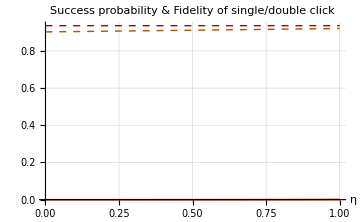

```mathematica
PlotPFusingParameterSets[SetNVnoGateError]
```

Plot using `SetNVnoPg1`

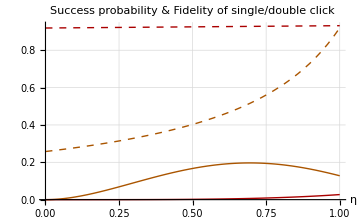

```mathematica
PlotPFusingParameterSets[SetNVPg1]
```

Plot using `SetOnlyη`

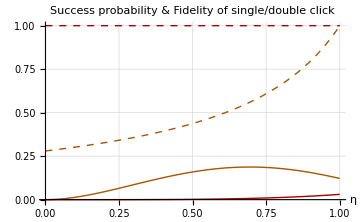

```mathematica
PlotPFusingParameterSets[SetOnlyη]
```